## 3-body interaction of test particle in binary (with specific goal to model “spray” of ejecta seen in etaCar)

```mathematica
Today
```

Day: Sun 16 Jun 2019

## Direct Integration using simple Euler method

### Analytic binary orbit solver for two main stars

Input parameters are:
m2     ; mass ratio of bullet star to target star
pbin     ; perod of binary orbit, in units of period of test particle's circular orbit 
rmin     ; minimum stellar separation at periastron 

These are then used to compute:
a =(pbin*(1+m2))^(2/3)    ; semi-major axis
       ϵ = 1-rmin/a                    ; eccentrity needed to give periastron (1-ϵ)a = rmin

#### Code

```mathematica
tofth[θ_]:=(2 ArcTan[(√(1-ϵ) Tan[θ/2])/(√(1+ϵ))]-(ϵ √(1-ϵ^2) Sin[θ])/(1+ϵ Cos[θ]))/(2 π);
rect[t_]:=Block[{ttt},
ttt=FractionalPart[t];
If[Abs[ttt]>1/2,ttt=ttt-Sign[ttt]];
ttt
];

thoft[t_]:=
 θ/.FindRoot[tofth[θ]==rect[t],{θ,-π,π}];

rhat[θ_]  := {Cos[θ],Sin[θ]};
rmag[θ_]  :=(a (1-ϵ^2))/(1+ϵ Cos[θ]);
rvec[θ_]  :=rmag[θ] rhat[θ];
rvect[t_]:=rvec[thoft[t/pbin+0.5]];
x1[t_]:=-rvect[t ][[1]]/(1+1/m2);
y1[t_]:=-rvect[t][[2]]/(1+1/m2);
x2[t_]:=rvect[t][[1]]/(1+m2);
y2[t_]:=rvect[t][[2]]/(1+m2);

(* get speeds from numerical differentiation *)
dtfac=50/π;  (* dtfac = 1/(2π*dt) with dt=0.01 *)
u1[t_]:=dtfac(x1[t+0.005]-x1[t-0.005]);
v1[t_]:=dtfac(y1[t+0.005]-y1[t-0.005]);
u2[t_]:=dtfac(x2[t+0.005]-x2[t-0.005]);
v2[t_]:=dtfac(y2[t+0.005]-y2[t-0.005]);
xy1vec[tt_]:={x1[tt],y1[tt]};
xy2vec[tt_]:={x2[tt],y2[tt]};
```

#### Check how close target would be to critical rotation if locked to periastron passage of bullet

```mathematica
m2=1.;   (* mass ratio of bullet star to target star *)
pbin=2; (* perod of binary orbit, in units of period of test particle's circular orbit *)
tmax= pbin; (* final time for integration *)
a=(pbin*(1+m2))^(2/3) ;(* semi-major axis, given the period and mass ratio, in units of test particle orbit *)
rmin=1.4; (* minimum stellar separation at periastron *)
ϵ=1-rmin/a; (* eccentrity needed to give periastron (1-ϵ)a = rmin *)
tt=pbin/2;
{x1[tt],u1[tt],v1[tt],x2[tt],u2[tt],v2[tt]}
xrel=x2[tt]-x1[tt]
vrel=v2[tt]-v1[tt]
orel=vrel/xrel
```

{-0.7,0.,-1.01549,0.7,0.,1.01549}

1.4

2.03099

1.4507

### 3-Body calculations

#### Set parameters for 3-body integration

```mathematica
m2=1.;   (* mass ratio of bullet star to target star *)
pbin=30; (* perod of binary orbit, in units of period of test particle's circular orbit *)
rmin=1.1; (* minimum stellar separation at periastron *)

tmax= pbin; (* final time for integration *)

thi=0 Degree; (* range of initial longitudes (tho) to compute *)
dth=10 Degree;
thf=360 Degree;
nth=1+(thf-thi)/dth;

a=(pbin*(1+m2))^(2/3) (* semi-major axis, given the period and mass ratio, in units of test particle orbit *)
ϵ=1-rmin/a; (* eccentrity needed to give periastron (1-ϵ)a = rmin *)
```

15.3262

#### Code for simple Euler integration

```mathematica
ndt=200;        (* # steps within test particle orbital period *)
dt=1./ndt;  (* step in fractions of test particle orbital period *)
dtn=2π dt;  (* normalized time step to allow u,a,t in all be units of test particle values *)
xy1dat=Table[xy1vec[tt],{tt,0,tmax,dt}]; (* collect time series for stellar position vectors *)
xy2dat=Table[xy2vec[tt],{tt,0,tmax,dt}];
xy21dat=xy2dat-xy1dat;
```

```mathematica
t=0;
xydats={};
thofs={};
plts={};
xmax=a+1;
Do[
xo=Cos[tho];yo=Sin[tho];uo=-yo;vo=xo;x=xo+x1[0];y=yo+y1[0];u=uo+u1[0];v=vo+v1[0];dat={};r1mag=1;AppendTo[dat,{t,x,y,u,v,0,0,r1mag}];
Do[
dx1=x-x1[t];dx2=x-x2[t];dy1=y-y1[t];dy2=y-y2[t];r1sq=dx1^2+dy1^2;r2sq=dx2^2+dy2^2;gx1=-dx1/r1sq^(3/2);gx2=-(m2 dx2)/r2sq^(3/2);gy1=-dy1/r1sq^(3/2);gy2=-(m2 dy2)/r2sq^(3/2);u=u+(gx1+gx2) dtn;v=v+(gy1+gy2) dtn;x=x+u dtn;y=y+v dtn;r1mag=√r1sq;AppendTo[dat,{t,x,y,u,v,gx1+gx2,gy1+gy2,r1mag}],{t,dt,tmax,dt}];xydat=Transpose[{Transpose[dat]⟦2⟧,Transpose[dat]⟦3⟧}];AppendTo[xydats,xydat];AppendTo[thofs,{tho/°,ArcTan[x,y]/°}];
AppendTo[plts,
ListPlot[{xydat,xy1dat,xy2dat},PlotStyle->{Black,Green,Red},AspectRatio->Automatic,Frame->True,FrameLabel->{"x","y"},PlotLabel->{"m_b/m_t=",m2,"r_min=",(1-ϵ)a,"θ_o=",tho,"dt=",dt},Joined->True,PlotRange->{{-xmax,xmax},{-xmax/2,xmax/2}}]
];
,{tho,thi,thf,dth}];
```

### Results and Plots

#### Backscattering result

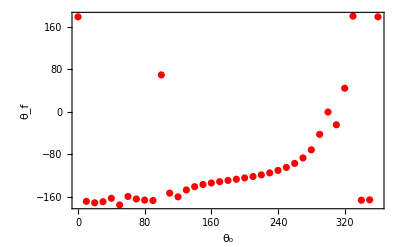

```mathematica
plt1=ListPlot[thofs,Frame->True,FrameLabel->{"θ_o","θ_f"},Joined->False,PlotStyle->Red];plt2=ListPlot[ Table[ArcTan[xylast[[i]][[1]],xylast[[i]][[2]]]/Degree,{i,1,Length[xylast]}],DataRange->{0,360},Frame->True,FrameLabel->{"θ_o","θ_f"},Joined->True,PlotRange->{-180,180}];
plt2a=ListPlot[ Table[ArcTan[xylast[[i]][[1]],xylast[[i]][[2]]]/Degree,{i,1,Length[xylast]}],DataRange->{0,360},Frame->True,FrameLabel->{"θ_o","θ_f"},Joined->False,PlotRange->{-180,180}];
Show[plt1]
```

```mathematica
Manipulate[
Show[plts[[i]]],
{{i,1},1,Length[plts],1,Appearance->"Open",AutorunSequencing->1
,SaveDefinitions->True}
]
```

```mathematica
Manipulate[
Show[plts1[[i]]],
{{i,1},1,36,1,Appearance->"Open"},AutorunSequencing->1
,SaveDefinitions->True
]
```

#### Array of result plots

GraphicsGrid::list: … is not a list of lists.

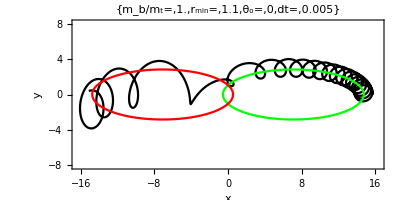
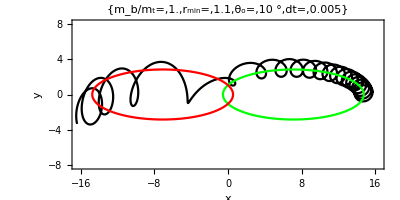
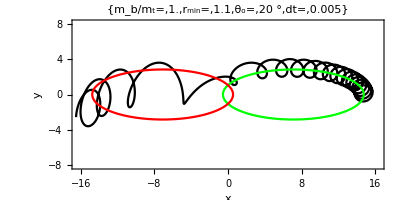
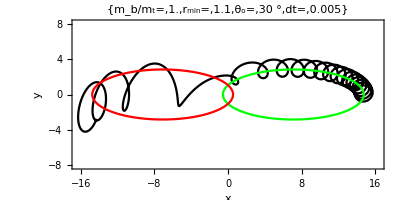
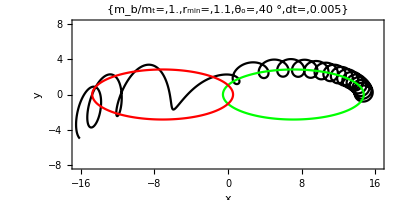
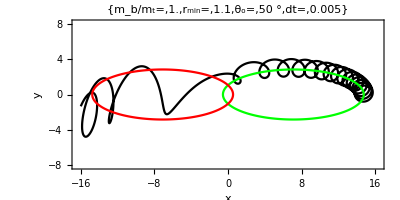
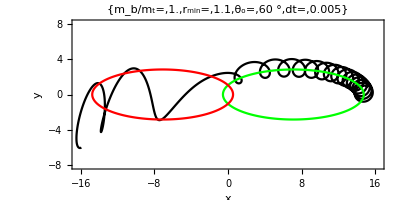
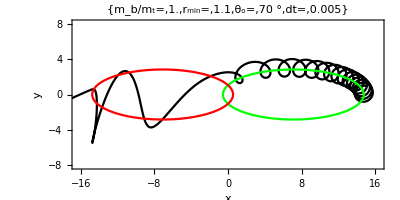
GraphicsGrid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]

```mathematica
GraphicsGrid[plts]
```

#### Time resolution test for dt={0.001, 0.0025,0.005}

```mathematica
GraphicsRow[restestplts]
```

GraphicsGrid::list: {restestplts} is not a list of lists.

GraphicsGrid[{restestplts}]

#### plot array saves

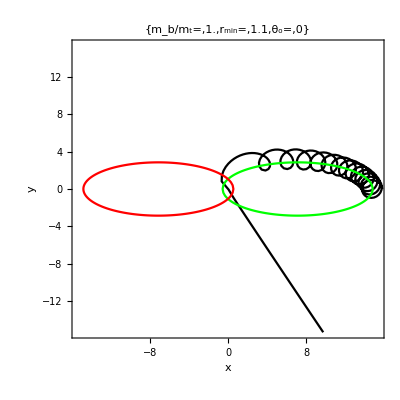
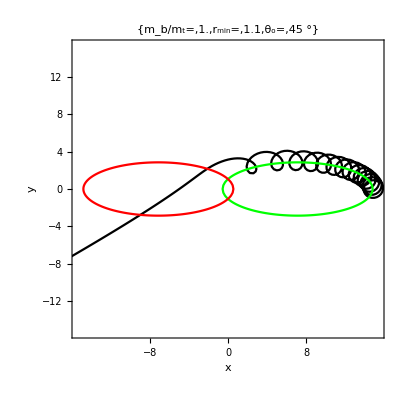
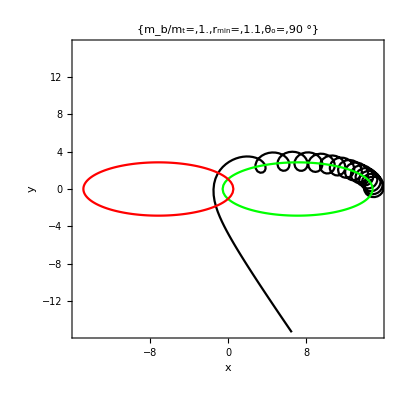
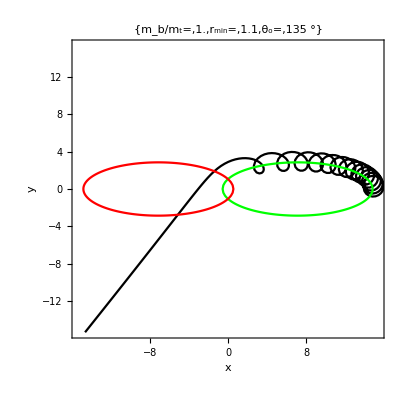
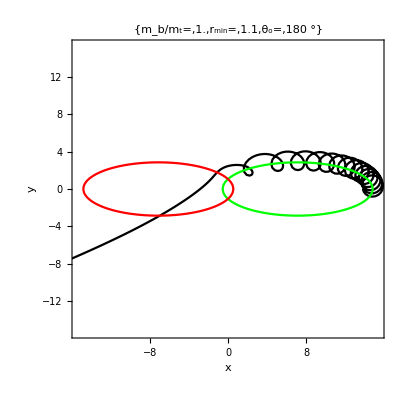
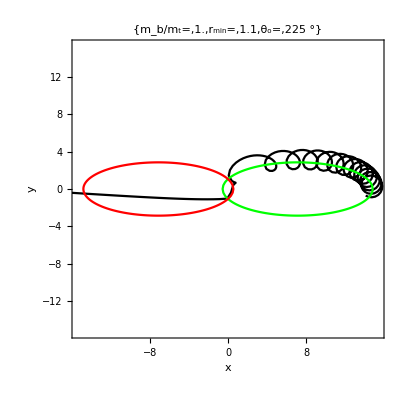
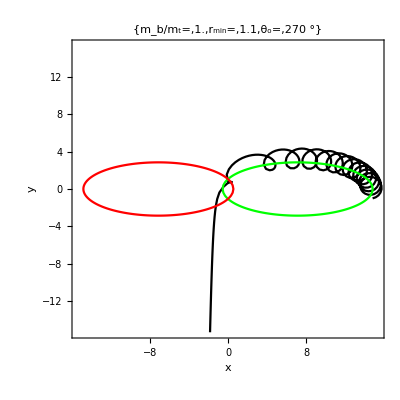
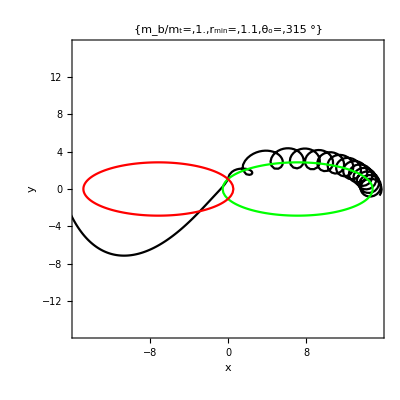
```mathematica
plts={{-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-},{
-Graphics-,
-Graphics-,
-Graphics-,
-Graphics-}};
```

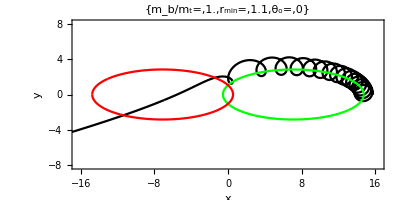
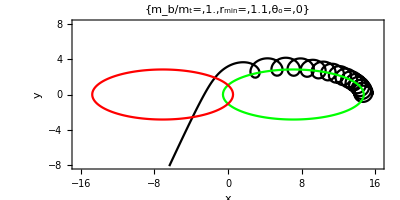
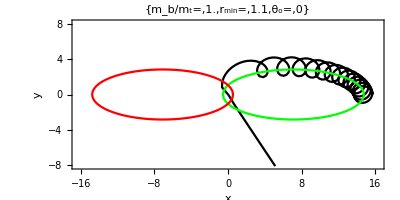
```mathematica
restestplts={-Graphics-,
-Graphics-,
-Graphics-};
```

```mathematica
6
```

6

#### Plots in frame of target star

```mathematica
nt=Length[xydat];
itperias=1+ndt*pbin/2;
it0=itperias-ndt;
itf=itperias+ndt/2;
max=5;
cir=Graphics[Circle[{0,0}]];
tmp2=ListPlot[xy21dat,PlotStyle->{{PointSize[Small],Blue}}];
dat=xydats-Table[xy1dat,{ith,1,nth}];
Manipulate[
tho=thi+(ith-1)dth;
tmp1=ListPlot[dat[[ith]],PlotStyle->{PointSize[Tiny],Red},AspectRatio->Automatic,Frame->True,FrameLabel->{"x","y"},PlotLabel->{"m_b/m_t=",m2,"r_min=",(1-ϵ)a,"θ_o=",tho,"t=",dt*(it-1)},Joined->False,PlotRange->{{-max,Min[max,2]},{-max,max}},GridLines->Automatic];
Show[
tmp1,tmp2,cir,
ListPlot[{dat[[ith,it]]},PlotStyle->{PointSize[Large],Black}],
ListPlot[{xy21dat[[it]]},PlotStyle->{PointSize[Large],Blue}]
],
{{it,itperias},it0,itf,4,
Appearance->"Open",AutorunSequencing->1,SaveDefinitions->True},
{{ith,1},1,37,1,
Appearance->"Open",AutorunSequencing->1,SaveDefinitions->True}
]
```

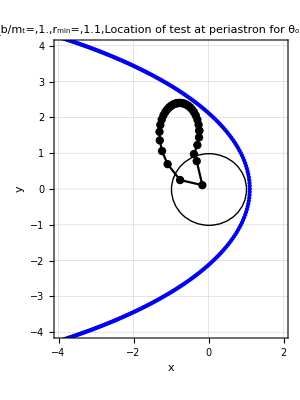

```mathematica
max=4;
tmp=Table[xydats[[it]][[3001]]-xy1dat[[3000]],{it,1,37}];
Show[ListPlot[
tmp,PlotStyle->{PointSize[Medium],Black},Joined->True,Mesh->All,
AspectRatio->Automatic,Frame->True,FrameLabel->{"x","y"},PlotLabel->{"m_b/m_t=",m2,"r_min=",(1-ϵ)a,"Location of test  at periastron for θ_o=0,360,10"},PlotRange->{{-max,Min[max,2]},{-max,max}},GridLines->Automatic]
,tmp2,cir]
```